NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 12 : Use ML-inequality to show that |∫_C 1/(z^2+1)ⅆz|<= 1/5 ,where C is the line segment form 2 to 2 + ⅈ. While solving, represent the distance from the point z to the points ⅈ and -ⅈ, respectively

1/5

1

An upper bound to the absolute value of the integral |∫_C 1/z^2ⅆz| is found to be 1/5.

{2,0.465359}

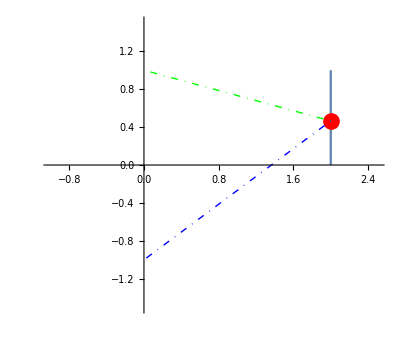

```mathematica
f[z_]:=1/(z^2+1)
c[t_]:=2+ⅈ t
k[t_]:=ComplexExpand[f[c[t]]]
r[t_]:=Refine[Re[k[t]],t ∈ Reals]
s[t_]:=Refine[Im[k[t]],t ∈ Reals]
A[t_]:=Simplify[√(s[t]^2+r[t]^2)]
M=MaxValue[{A[t],0<=t<=1},t]
L=∫_0^1 Abs[c'[t]]ⅆt
Print["An upper bound to the absolute value of the integral |∫_C 1/z^2ⅆz| is found to be ",M*L,"."]
p={2,RandomReal[{0,1}]}
a=ParametricPlot[{Re[c[t]],Im[c[t]]},{t,0,1},PlotRange->{{-1,2.5},{-1.5,1.5}}];
b=Graphics[{Red,PointSize[0.03],Point[p],Green,DotDashed,Line[{p,{0,1}}],Blue,DotDashed,Line[{p,{0,-1}}]}];
Show[a,b]
```